```mathematica
Clear[p]
```

```mathematica
p[x_,k_,maxA0_,s_]:=s PDF[ExponentialDistribution[k],-(x-maxA0)]
```

```mathematica
p[-10,5,9,1/2]
```

5/(2 ⅇ^95)

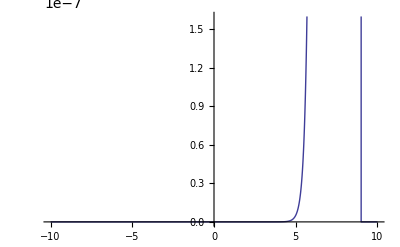

```mathematica
Plot[p[x,5,9,1/2],{x,-10,10}]
```

```mathematica
p[x,k,maxA0,s]
```

ⅇ^(-k (maxA0-x)) k s

```mathematica
Integrate[p[x,k,maxA0,s],{x,-Infinity,maxA0},Assumptions->0<1/k<maxA0&&0<s≤1]
```

s

```mathematica
Integrate[x p[x,k,maxA0,s],{x,-Infinity,maxA0},Assumptions->0<1/k<maxA0&&0<s≤1]
```

((-1+k maxA0) s)/k

```mathematica
Solve[((-1+k maxA0) s)/k==μ,k]
```

{{k→s/(maxA0 s-μ)}}

```mathematica
Integrate[x p[x,s/(maxA0 s-μ),maxA0,s],{x,-Infinity,maxA0},Assumptions->0<(maxA0 s-μ)/s<maxA0&&0<s≤1]
```

μ

```mathematica
Reduce[0<(maxA0 s-μ)/s<maxA0&&0<s≤1,μ,Reals]
```

maxA0>0&&0<s≤1&&0<μ<maxA0 s

```mathematica
Simplify[-(maxA0 s-s μ)/(maxA0 s-μ)/(μ-maxA0)]
```

s/(maxA0 s-μ)